Шумы при сдвиге частот Δφ=0:
Через функции!

```mathematica
SVDVector[x_, a_?NumberQ] := Transpose[SingularValueDecomposition[x][[1; 3]]][[a]];
```

```mathematica
AbsFourier[x_]:=Abs[Take[Fourier[x,FourierParameters->{-1, -1}],{1,Length[x]/2+1}]]
```

```mathematica
NumPlace[x_]:=Position[AbsFourier[x],Max[AbsFourier[x]]][[1,1]]
```

```mathematica
FreqList[x_]:=Table[1.0*b/Length[x],{b,0,Length[x]-1}]
```

```mathematica
Freq[x_]:=FreqList[x][[NumPlace[x]]]
```

```mathematica
TruePlot[x_]:=ListPlot[Transpose[{FreqList[x][[1;;NumPlace[x]+4]],AbsFourier[x][[1;;NumPlace[x]+4]]}],PlotRange->All,PlotStyle->Red,FrameLabel->{"ν","A, mm"}]
SetOptions[{Plot,ListPlot,ListLinePlot,ListLogPlot},PlotRange->Full,(*PlotRangePadding->{None,Automatic},*)Axes->False,Frame->True,GridLines->Automatic,GridLinesStyle->Directive[Gray,Dashed],BaseStyle->{FontFamily->"Courier New",FontSize->14,Bold},ImageSize->500,PlotStyle->PointSize[0.01]];
```

```mathematica
sig1=Table[Cos[2 π *0.3* k] +(Random[]-0.5),{k,1,1500}];
sig2=Table[0.8*(Cos[2 π *0.3* k] +(Random[]-0.5)),{k,1,1500}];
sig3=Table[0.95*(Cos[2 π *0.3* k] +(Random[]-0.5)),{k,1,1500}];
sig4=Table[0.85*(Cos[2 π *0.3* k] +(Random[]-0.5)),{k,1,1500}];
SigM=Transpose[{{sig1},{sig2},{sig3},{sig4}}];
```

0.3

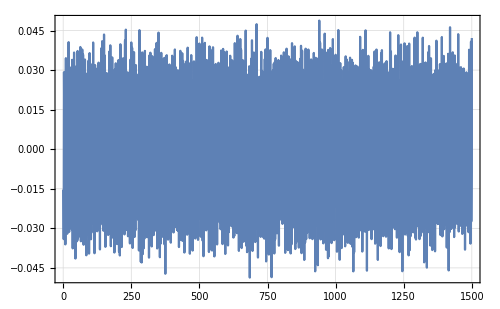

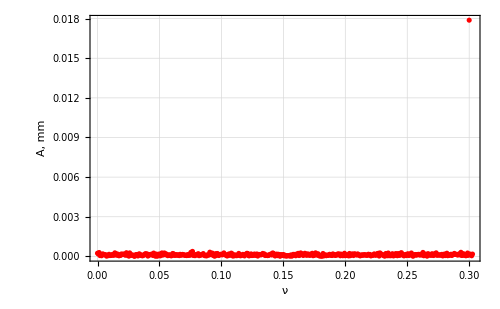

```mathematica
SVDVector1=SVDVector[SigM,1];
Freq[SVDVector1]
ListPlot[SVDVector1,Joined->True,PlotRange->All]
TruePlot[SVDVector1]
```

0.006

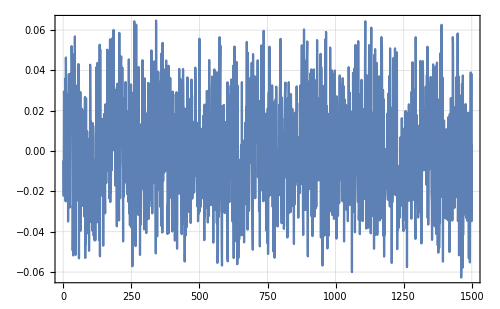

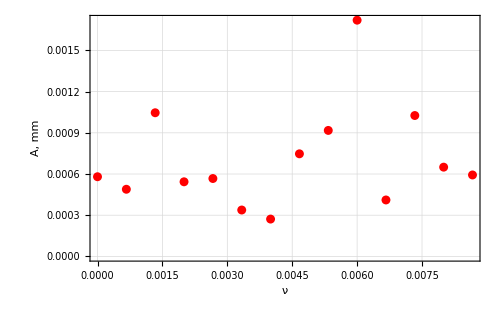

```mathematica
SVDVector2=SVDVector[SigM,2];
Freq[SVDVector2]
ListPlot[SVDVector2,Joined->True,PlotRange->All]
TruePlot[SVDVector2]
```

```mathematica
SetDirectory[NotebookDirectory[]]
```

F:\Загрузки\Диплом

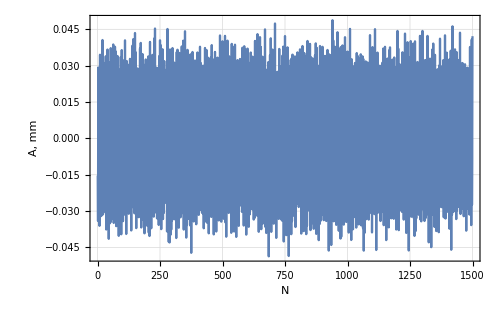

-Graphics-

-Graphics-

```mathematica
Pic1 = ListPlot[SVDVector1,Joined->True,PlotRange->All,FrameLabel->{"N","A, mm"}]
Pic2 = TruePlot[SVDVector1]
Pic3 = TruePlot[SVDVector2]
```

(*Export["Sig1.png",Pic1]
Export["PCA1.png",Pic2]
Export["PCA2.png",Pic3]*)